### Константы

```mathematica
If[True,
A            =- 0.024 ;
B            = 1.69 ;
CC          = 0.5 ;
α            = 10^-5                 (* K^-1 *);
Subscript[T, 0]          = 300                  (* K *);
Subscript[T, avg]       = 300                  (* K *);
Young   = 1.75 * 10^11  (* Па *);
σf          = 1.1 * 10^8      (* Па *);
ϵf          = 0.000628571 ;
l            = 10                     (* Длина стержня *);
Subscript[T, f]          =22.2                      (* Конечный момент времени *); 
Subscript[h, t]            = 0.05              (* Шаг времени *);
a            = 50                     (* Просто константа *);
n            =  10                      (* Число узлов сетки *);
Subscript[h, x]          = l/(n-1)                                       (* Шаг сетки *);
];
```

### Определение функций распределения температуры в пространстве и времени

```mathematica
F[x_] := a Sin[(π x)/l];
Subscript[T, 1][x_, t_] := Subscript[T, avg] + F[x]t Sin[t];
Subscript[T, 2][ x_, t_ ] := Subscript[T, avg] + F[x] Cos[π t^2](t+1);
TT = Subscript[T, 1];
```

Тепловые деформации

```mathematica
Subscript[ϵ, t] [x_,tt_] := α(TT[x, tt] - Subscript[T, 0]);
```

```mathematica
Subscript[u, analytical] = 
First[Flatten[
DSolve[{
D[D[u[x,t], {x, 1}]-Subscript[ϵ, t][x, t], {x, 1}]== 0,
u[0, t] == 0, 
u[l, t] == 0
},u[x,t],{x, t}]]
]⟦2⟧  // FullSimplify
```

-(t (-5+x+5 Cos[(π x)/10]) Sin[t])/(1000 π)

### Численное решение (метод конечных разностей)

```mathematica
points = Table[i*Subscript[h, x], {i, 0, n-1}];
στ = Table[0,{i, 1, n}];                                     (* значения напряжений во временном слое τ *)
σfv = Table[σf,{i, 1, n}];                                (* значения переменных пределов прочности *)
ϵτ = Table[0,{i, 1, n}];                                            (* значения полных деформаций во временном слое τ *)
ϵe = Table[0,{i, 1, n}];                                     (* значения упругих деформаций во временном слое τ *)
ϵT = Table[0,{i, 1, n}];                                            (* значения температурных деформаций во врменном слое τ *) 
ϵcrk = Table[0,{i, 1, n}];                                        (* значения деформаций за счет трещин *) 
Tτ = Table[0,{i, 1, n}];                                            (* значения температуры во временном слое τ *) 
Subscript[balance, normal] [x_,k_]:= Young x;                             (* функция, подставляемая в условие равновесия при напряжениях, меньших предельных *) 
Subscript[dbalance, normal][xx_, k_] := D[Subscript[balance, normal][x, k], {x, 1}] /. x-> xx;
Subscript[balance, crack][x_,k_]:=  σfv⟦k⟧(A + B ⅇ^(-CC x/ϵf));   (* функция, подставляемая в условие равновесия при напряжениях, больших предельных *) 
Subscript[dbalance, crack][xx_,k_] := D[Subscript[balance, crack][x, k], {x, 1}] /. x-> xx;
balances =  Table[0,{i, 1, n}];                              (* функции равновесий на временном слое τ *) 
left = Table[0,{i, 1, n}];                           (* линеаризованные уравнения, решениями которых являются перемещения на временном слое τ *) 
right = Table[0,{i, 1, n}];                           (* линеаризованные уравнения, решениями которых являются перемещения на временном слое τ *) 
shifts = Table[0,{i, 1, n}];                                 (* сами перемещения *) 
cracking = Table[False,{i, 1, n}];                   (* нужно ли менять предел прочности*)
data = {};
debug = True;
```

Подготавливаем левую часть линеаризованной системы. При решении СЛАУ она будет оставаться постоянной, меняется только правая часть на каждой итерации метода Ньютона

```mathematica
left ={{1}~Join~ConstantArray[0, n-1]}~Join~Table[
Table[
If[Between[j, {i-1, i+1}], 
If[j == i, -2, 1],0
], 
{j, 1, n}
],
{i, 2, n-1}]~Join~{ConstantArray[0, n-1]~Join~{1}};
For[τ = 0,τ≤Subscript[T, f],τ=τ+Subscript[h, t],
If[False, Break[]];
temp = {};
For [i = 1, i≤ n, ++i,
Tτ⟦i⟧= TT[points⟦i⟧, τ];
ϵT⟦i⟧ = Subscript[ϵ, t][points⟦i⟧, τ];
memory =Young*( ϵτ⟦i⟧ - ϵT⟦i⟧ - ϵcrk⟦i⟧); 
balances⟦i⟧ = If[memory < σfv⟦i⟧, 
cracking⟦i⟧ = False;Subscript[balance, normal],
cracking⟦i⟧ = True; Subscript[balance, crack]
];
];
iterations = 0;
While[Norm[(shifts - previous)/(Norm@previous + 10^-20)] ≥ 10^-5 || iterations == 0,
++iterations; 
For[i = 2, i < n, ++i,
Subscript[nonElastic, i] = If[cracking⟦i⟧, ϵT⟦i⟧, ϵT⟦i⟧ + ϵcrk⟦i⟧]; Subscript[nonElastic, i-1] = If[cracking⟦i⟧, ϵT⟦i-1⟧, ϵT⟦i-1⟧ + ϵcrk⟦i-1⟧];
Subscript[v, i]= (shifts⟦i+1⟧ - shifts⟦i⟧)/Subscript[h, x] - Subscript[nonElastic, i]*If[debug, 1, 0]; Subscript[v, i-1]=(shifts⟦i⟧ - shifts⟦i-1⟧)/Subscript[h, x] - Subscript[nonElastic, i-1]*If[debug, 1, 0];
If[cracking⟦i⟧,
Subscript[dσ, i] = Subscript[dbalance, crack][Subscript[v, i], i]; Subscript[dσ, i-1] = Subscript[dbalance, crack][Subscript[v, i-1], i], 
Subscript[dσ, i] = Subscript[dbalance, normal][Subscript[v, i], i]; Subscript[dσ, i-1] = Subscript[dbalance, normal][Subscript[v, i-1], i];
];
right⟦i⟧ = Subscript[h, x](Subscript[v, i] +  Subscript[nonElastic, i]*If[debug, 1, 0]) - Subscript[h, x]( Subscript[v, i-1] +  Subscript[nonElastic, i-1]*If[debug, 1, 0]) - (Subscript[h, x] balances⟦i⟧[Subscript[v, i], i])/Subscript[dσ, i]+ (Subscript[h, x] balances⟦i⟧[Subscript[v, i-1], i])/Subscript[dσ, i-1];
];
previous = shifts;
shifts = Flatten@LinearSolve[left, right];
];
For [i=1, i< n, ++i,
ϵτ⟦i⟧ = (shifts⟦i+1⟧ - shifts⟦i⟧)/Subscript[h, x];
If[cracking⟦i⟧,
σfv⟦i⟧=balances⟦i⟧[ϵτ⟦i⟧ - ϵT⟦i⟧, i]; στ⟦i⟧ = σfv⟦i⟧; ϵe⟦i⟧ = στ⟦i⟧/Young; ϵcrk⟦i⟧ = ϵτ⟦i⟧ - ϵT⟦i⟧ - ϵe⟦i⟧ ,
ϵe⟦i⟧ = ϵτ⟦i⟧ -ϵT⟦i⟧-ϵcrk⟦i⟧; στ⟦i⟧ = balances⟦i⟧[ϵe⟦i⟧, i]; 
];
AppendTo[temp, {τ, Tτ⟦i⟧, στ⟦i⟧, ϵτ⟦i⟧, ϵτ⟦i⟧-ϵT⟦i⟧, ϵcrk⟦i⟧, ϵe⟦i⟧}]
];
AppendTo[data, temp];
];
```

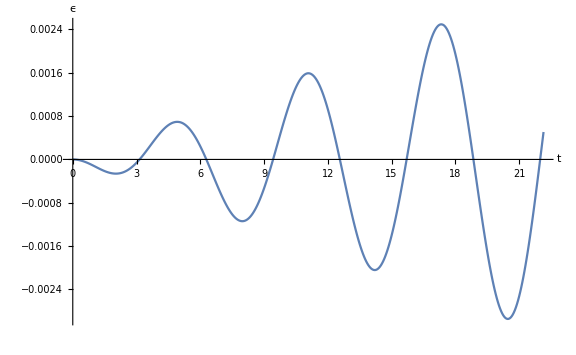

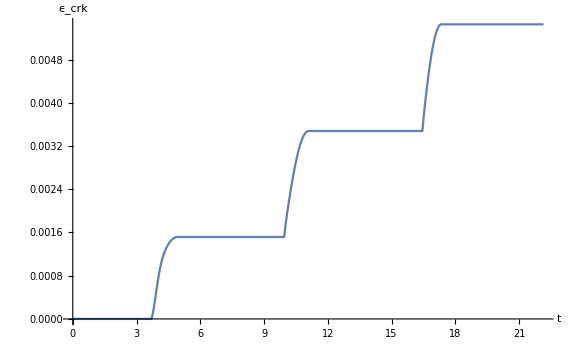

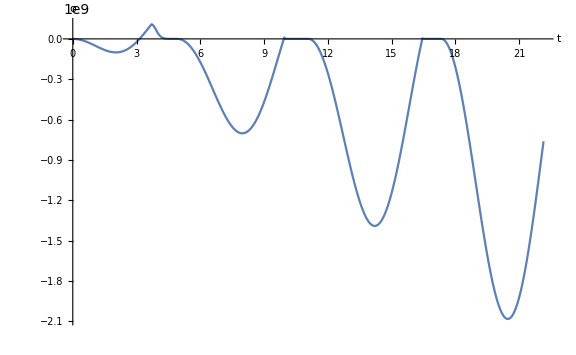

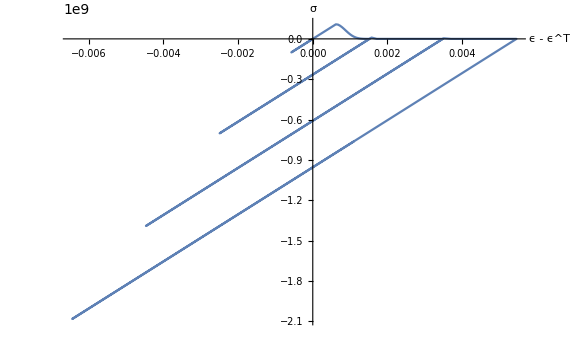

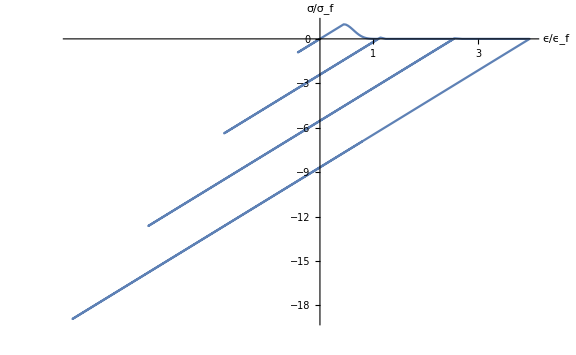

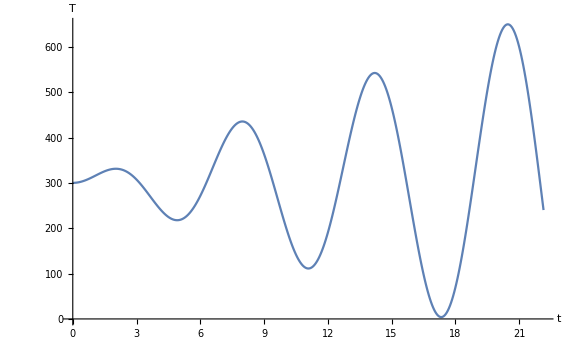

```mathematica
node = 2; 
tϵ = ListPlot[Table[{data⟦τ, node, 1⟧, data⟦τ, node, 4⟧}, {τ, 1,IntegerPart@ (Subscript[T, f]/Subscript[h, t])}], Joined->True,ImageSize->Large, AxesLabel->{"t", "ϵ"},AxesStyle->Black]
tϵcrk = ListPlot[Table[{data⟦τ, node, 1⟧, data⟦τ, node, 6⟧}, {τ, 1,IntegerPart@ (Subscript[T, f]/Subscript[h, t])}], Joined->True,ImageSize->Large,  AxesLabel->{"t", "ϵ_crk"},AxesStyle->Black]
tσ = ListPlot[Table[{data⟦τ, node, 1⟧, data⟦τ, node, 3⟧}, {τ, 1,IntegerPart@ (Subscript[T, f]/Subscript[h, t])}], Joined->True,ImageSize->Large,  AxesLabel->{"t", "σ"},AxesStyle->Black]
dϵσ = ListPlot[Table[{data⟦τ, node, 5⟧, data⟦τ, node, 3⟧}, {τ, 1,IntegerPart@ (Subscript[T, f]/Subscript[h, t])}], Joined->True, ImageSize->Large,AxesLabel->{"ϵ - ϵ^T", "σ"},AxesStyle->Black]
normdϵσ = ListPlot[Table[{data⟦τ, node, 4⟧/ϵf, data⟦τ, node, 3⟧/σf}, {τ, 1,IntegerPart@ (Subscript[T, f]/Subscript[h, t])}], Joined->True,ImageSize->Large, Ticks->{Table[i,{i,1,10}], Automatic},AxesLabel->{"ϵ/ϵ_f", "σ/σ_f"},AxesStyle->Black]
tT = ListPlot[Table[{data⟦τ, node, 1⟧, data⟦τ, node, 2⟧}, {τ, 1,IntegerPart@ (Subscript[T, f]/Subscript[h, t])}], Joined->True, ImageSize->Large,AxesLabel->{"t", "T"},AxesStyle->Black ]
```

### Сохраняем графики

```mathematica
If[False, 
SetDirectory[NotebookDirectory[]];
options =StringJoin[ToString@TT~StringJoin~"/", StringJoin["h_", ToString[h] ~StringJoin~"_"], StringJoin["tau_", ToString[τ]]];
With[
{directory=FileNameJoin[{ParentDirectory@NotebookDirectory[], StringJoin["LaTeX/pic/",options ]}]},
Switch[FileType[directory],
None,CreateDirectory[directory],
Directory, Print["Overriding files in directory: "~StringJoin~directory]
];
Export[FileNameJoin[{directory, "epsilon(t).pdf"}], tϵ];
Export[FileNameJoin[{directory, "epsilon_crk(t).pdf"}], tϵcrk];
Export[FileNameJoin[{directory, "sigma(t).pdf"}], tσ];
Export[FileNameJoin[{directory, "sigma(epsilon).pdf"}], dϵσ];
Export[FileNameJoin[{directory, "norm_sigma(epsilon).pdf"}], normdϵσ];
Export[FileNameJoin[{directory, "T(t).pdf"}], tT];
]
];
```